# Controlled Power

Episodes 17 and 19. ControlledGate

Episode 34. ControlledPower

## What is it?

The controlled-power of unitary operator U is given by

x_1 x_2…x_n⊗ψ↦x_1 x_2…x_n⊗(U^x ψ) ,

where x:=(x_1 x_2(…x)_n)_2=x_1 2^(n-1)+x_2 2^(n-2)+…+x_n.

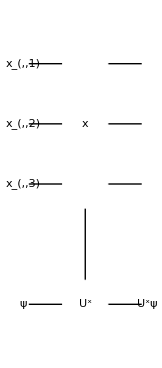

Figure 1. Quantum circuit for the controlled-power of unitary U, x_1 x_2…x_n⊗ψ↦x_1 x_2…x_n⊗(U^x ψ), where x:=(x_1 x_2(…x)_n)_2=x_1 2^(n-1)+x_2 2^(n-2)+…+x_n.

## Basic Example

```mathematica
Let[Qubit,S,T]
```

```mathematica
$n=3;
SS=S[Range[$n],$]
```

```mathematica
Let[Real,ϕ]
```

```mathematica
op=ControlledPower[SS,Phase[ϕ,T[3]]]
qc=QuantumCircuit[ProductState[T->{1,1}],op,
"Invisible"->S[$n+1/2],"PortSize"->{2,1}]
```

```mathematica
bs=Basis[SS]
```

```mathematica
out=qc**bs;
Thread[bs->out]//TableForm
```

## More Interesting Example

```mathematica
Let[Qubit,S,T]
```

```mathematica
$n=3;
kk=Range[$n];
SS=S[kk,$]
```

```mathematica
Let[Real,ϕ]
```

```mathematica
op=ControlledPower[SS,Phase[ϕ,T[3]]];
qc=QuantumCircuit[Ket[SS->0,T->1],
S[kk,6],"Spacer",op,
"Invisible"->S[$n+1/2],"PortSize"->{2,1}]
```

```mathematica
out=Elaborate[qc]
```

```mathematica
KetFactor[out,T]
```

```mathematica
KetDrop[out,T]
```

## Implementation with Elementary Gates

```mathematica
$n=3;
SS=S[Range[$n],$]
```

```mathematica
op=ControlledPower[SS,Phase[ϕ,T[3]]];
qc=QuantumCircuit[op,"Invisible"->S[$n+1/2]]
```

```mathematica
new=Expand[qc]
```

## Summary

### Keywords

Controlled-power of unitary operator

Controlled-unitary gate

### Functions

ControlledPower

ControlledGate

### Related Links

Section 4.3 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Phase Estimation